### Plot style

```mathematica
SetOptions[{Plot, ListPlot, ListLinePlot, ListLogPlot, ListLogLogPlot}, {BaseStyle -> {FontFamily -> "Times", FontSize -> 18}, PlotStyle -> ColorData[108, "ColorList"], PlotRange -> All, Frame -> True, FrameLabel -> {"R/n^2", "E/n^-3"}, GridLines -> Automatic, PlotLegends -> "Expressions", ImageSize -> Medium}];
SetOptions[{ListDensityPlot, ListPlot3D}, {BaseStyle -> {FontFamily -> "Times", FontSize -> 18}, PlotRange -> All, AxesLabel -> {"R/n^2", "n", "E/n^-3Δ"}, ImageSize -> Medium}];
```

## Setup

### Documentation

We use the perturbative analytic form of the trilobite wavefunction and the f-state wave function as basis states:
|1⟩ = (N^-1 Σ_(l>3)^(n-1)ϕ_nl0^*(R)ϕ_nl0(r))^(1/2) = T(R,r)
|2⟩ = ϕ_n30(r)

With the interaction 
V= δ^3(r-R)

this results in the Hamiltonian matrix elements
H_11 = ⟨1|V|1⟩ = (T(R,R))^2 
H_22 = ⟨2|V|2⟩ = (ϕ_n30(R))^2 
H_12 = ⟨1|V|2⟩ = T(R,R)ϕ_n30(R)

### Atomic units conversion

#### energies are displayed in GHz

```mathematica
unit = 2 3.289841960355 10^6;
```

#### Boltzmann constant [T/J]

```mathematica
kB = 1.380649*10^(-23);
```

#### Bohr unit of length [m]

```mathematica
a0 = 5.29177210903*10^(-11);
```

#### time [s]

```mathematica
ts = 2.4188843265857*10^(-17);
```

#### velocity [m/s]

```mathematica
vms = 2.18769126364*10^6; (* =a0/ts *)
```

#### electron mass [kg]

```mathematica
me = 9.1093837015*10^(-31);
```

#### atomic mass in units of electron mass

```mathematica
M = 86.909180527*1822.888486192;(* atomic mass *)
```

#### temperatures from 10 nK to 0.1 K

```mathematica
T = Table[10^t, {t,-8,-1,1}];
```

#### corresponding velocities in atomic units

```mathematica
vs = Sqrt[3 kB T/(M/2 me)]/vms
```

{1.09515×10^-9,3.46317×10^-9,1.09515×10^-8,3.46317×10^-8,1.09515×10^-7,3.46317×10^-7,1.09515×10^-6,3.46317×10^-6}

#### velocities in Bohr per ns

```mathematica
vs/ts/10^9
```

{0.045275,0.143172,0.45275,1.43172,4.5275,14.3172,45.275,143.172}

#### momentum [kg m/s]

```mathematica
pkgms = 1.99285191410*10^(-24); (* =me a0/ts *)
```

#### momentum of a moving wave packet

```mathematica
ks = vs M/2
```

{0.00008675,0.000274328,0.0008675,0.00274328,0.008675,0.0274328,0.08675,0.274328}

### Wavefunctions

#### Radial hydrogenic wave function

```mathematica
U[n_,l_,r_] := Sqrt[(2/n)^3 ((n-l-1)!/(2n(n+l)!))] Exp[-r/n] (2(r/n))^l LaguerreL[n-l-1,2l+1,2(r/n)]
dU[n_,l_,r_] := D[x U[n,l,x],x] /. x->r
```

#### Radial quantum defect state wave function

```mathematica
W[n_,l_,r_] := 1/n/Sqrt[(n+l)! (n-l-1)!] WhittakerW[n,l+1/2,2r/n]/r
dW[n_,l_,r_] := D[x W[n,l,x],x] /. x->r
```

#### Angular wave function

```mathematica
Y[l_] := Sqrt[(2l+1)/(4π)]
```

#### Trilobite wave function

Alternative formulation for fractional n

```mathematica
TrilU[n_, r_] := Sqrt[(r(2n^2-r)(U[n,0,r]/n)^2+dU[n,0,r]^2)/(4π)]
TrilW[n_, r_] := Sqrt[(r(2n^2-r)(W[n,0,r]/n)^2+dW[n,0,r]^2)/(4π)]
Trilobite[n_, r_] := If[n∈Integers, TrilU[n,r], TrilW[n,r]]
```

However, for integer n, this is numerically more stable

```mathematica
Trilobite[n_, l0_, r_] := Sqrt[Sum[U[n,l,r]^2 Y[l]^2,{l,l0,n-1}]]
```

#### Quantum defect state wave function

Note that l_0 is the smallest l without quantum defect

```mathematica
q[n_, l0_, r_] := SetPrecision[W[n,l0-1,r] Y[l0-1], 70]
```

### Interaction

#### Semi-classical electron wave number

```mathematica
kin[r_, n_] = Sqrt[2(-(2n^2)^(-1) + 1/r)];
```

### Atomic species

#### lithium Li

quantum defects

```mathematica
δLi = {0.3995101,0.04717,0.002129};
δLi = {0.3995101,0.04717};
l0 = Length[δLi];
δ[l_] = If[l<l0,δLi[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -6.7+π/3 164.2Re[k];
```

#### sodium Na

quantum defects

```mathematica
δNa = {1.347964,0.855,0.015543};
l0 = Length[δNa];
δ[l_] = If[l<l0,δNa[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -5.9+π/3 162.7Re[k];
```

#### potassium K

quantum defects

```mathematica
δK= {2.1801985,1.712,0.277,0.010098};
l0 = Length[δK];
δ[l_] = If[l<l0,δK[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -15.0+π/3 290.6Re[k];
```

#### rubidium Rb

quantum defects

```mathematica
δRb = {3.1311804,2.65,1.347,0.0165192};
l0 = Length[δRb];
δ[l_] = If[l<l0,δRb[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -15.2+π/3 319.2Re[k];
```

or import the data from Stuttgart

```mathematica
As = Interpolation[Import["/home/frederic/Documents/Wolfram Mathematica/data/Rbscat.csv", "Data"][[All,{1,2}]]];
A[k_] = As[Re[k]];
```

#### cesium Cs

quantum defects

```mathematica
δCs = {4.049325,3.57,2.47,0.033392};
δCs = {0.049325};
l0 = Length[δCs];
δ[l_] = If[l<l0,δCs[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -21.8+π/3 401Re[k];
```

#### strontium Sr

quantum defects

```mathematica
δSr = {3.371,2.8824,2.662,0.1200001};
l0 = Length[δSr];
δ[l_] = If[l<l0,δSr[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -13.2+π/3 186Re[k];
```

#### rubidium Rb

quantum defects

```mathematica
δRb = {3.1311804,2.65,1.347,0.0165192};
l0 = Length[δRb];
δ[l_] = If[l<l0,δRb[[l+1]],0];
```

scattering length

```mathematica
A[k_] = -15.2+π/3 319.2Re[k];
```

or import the data from Stuttgart

```mathematica
As = Interpolation[Import["/home/frederic/Documents/Wolfram Mathematica/data/Rbscat.csv", "Data"][[All,{1,2}]]];
A[k_] = As[Re[k]];
```

#### Quantum defect energy offset

Note that l_0 is the smallest l without quantum defect

```mathematica
Δ[n_] = 1/2/n^2-1/2/(n-δ[l0-1])^2;
```

## Two-state model

### Parameters

```mathematica
n0 = 70;
R = Subdivide[16/10,22/10,200];
```

### Set up 2x2 matrix

```mathematica
Hamiltonian[n_, l_, r_] := With[{a=2π A[kin[r n^2,n]], t=Trilobite[n,l,r n^2], f=q[n,l,r n^2], e=Δ[n]}, n^3 a {{t^2, t f}, {t f, e/a+f^2}}]
```

### Diagonalization

```mathematica
Dia = Table[Hamiltonian[n0, l0, r], {r,R}];
Adia = Table[Eigenvalues[Dia[[i]]], {i,Length[Dia]}];
```

```mathematica
dt = Dia[[All,1,1]];
df = Dia[[All,2,2]];
do = Dia[[All,1,2]];
at = Adia[[All,1]];
af = Adia[[All,2]];
```

### Diabatic potentials

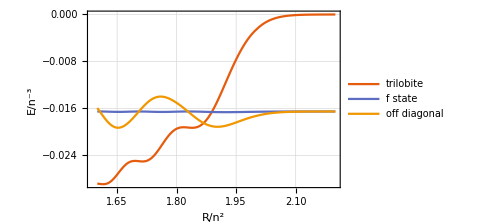

```mathematica
ListLinePlot[{{R, dt}ᵀ, {R, df}ᵀ, {R, 2 do+df}ᵀ}, PlotLegends->{"trilobite", "f state", "off diagonal"}]
```

#### Export diabatic potentials for mctdh

```mathematica
Export["/home/frederic/Documents/Wolfram Mathematica/data/grid.csv", N[R n0^2]];
Export["/home/frederic/Documents/Wolfram Mathematica/data/on1.csv", dt/n0^3];
Export["/home/frederic/Documents/Wolfram Mathematica/data/on2.csv", df/n0^3];
Export["/home/frederic/Documents/Wolfram Mathematica/data/off.csv", do/n0^3];
```

### Adiabatic potentials

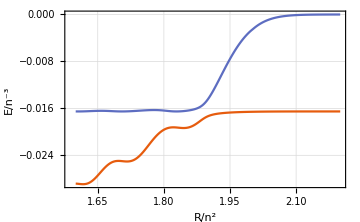

```mathematica
ListLinePlot[{{R, at}ᵀ, {R, af}ᵀ}]
```

## Semi-classical transition probabilities

### Clark' s transition probability (using the adiabatic representation)

The probability to cross from one to the other adiabatic potential at an avoided crossing at R_0 is given by
P=exp(-2π (ϵ_1(R_0)-ϵ_2(R_0))/(8vP_12(R_0))) = exp(-2π(ϵ_1(R_0)-ϵ_2(R_0))^2/(8v<ϕ_1|∇H|ϕ_2>))   
where v is the atomic velocity given as an external parameter

#### Position of the crossing

```mathematica
CrossingA = Ordering[Abs[Drop[at,100]-Drop[af,100]],1][[1]]+100
```

101

#### d = | ϵ1 - ϵ2 |

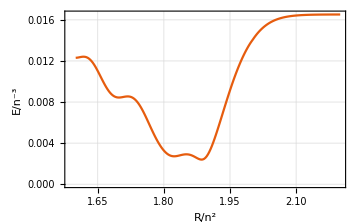

```mathematica
d = Interpolation[Abs[at-af]];
ListLinePlot[{{R,Abs[at-af]}ᵀ}]
```

#### Elements of H

```mathematica
H11 = Interpolation[dt];
H12 = Interpolation[do];
H22 = Interpolation[df];
```

#### Derivative H'

```mathematica
DH[r_] := {{H11'[r],H12'[r]},{H12'[r],H22'[r]}};
```

#### Eigenvectors ϕ

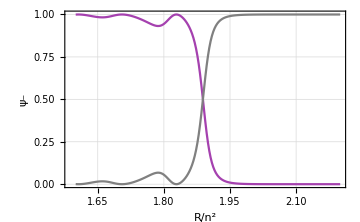

```mathematica
Φ = Table[Eigenvectors[Dia[[i]]], {i,Length[Dia]}];
a4 = ListLinePlot[Table[{R,Φ[[All,i,1]]^2}ᵀ,{i,2}], FrameLabel->{"R/n^2", "ψ_-"}, PlotStyle->{ColorData[108,"ColorList"][[4]], Gray}]
```

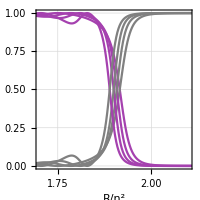

```mathematica
components = Show[a1,a2,a3,a4,PlotRange->{{1.7,2.1},Automatic},ImageSize->200,AspectRatio->1]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/components_v3.pdf",components];
```

#### Off-diagonal element of the P matrix

For the transition probability, we need the off-diagonal element of the P matrix, which is the derivative coupling element of the two adiabatic eigenstates 
P_12(R) = <ϕ_1|∇ϕ_2> = (ϵ_1(R)-ϵ_2(R))^-1<ϕ_1|∇H|ϕ_2>

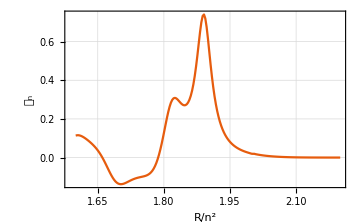

```mathematica
P12 = Table[Φ[[i,1]].DH[i].Φ[[i,2]]/d[i],{i,Length[R]}];
b4 = ListLinePlot[{{R,-10P12}ᵀ}, FrameLabel->{"R/n^2", "𝒫_n"}]
```

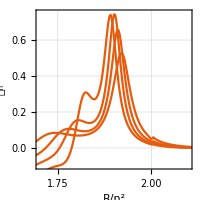

```mathematica
pmatrix = Show[b1,b2,b3,b4,PlotRange->{{1.7,2.1},{-0.1,0.75}},ImageSize->200,AspectRatio->1]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/pmatrix_v3.pdf",pmatrix];
```

```mathematica
Pmaximum = Ordering[Abs[Drop[P12,100]],-1][[1]]+100
```

101

#### Transition Probability

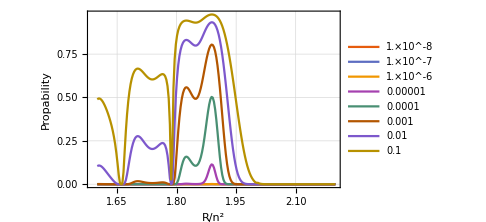

```mathematica
TransProbC[v_] = Exp[-2π Abs[(at-af)/n0^3]/(8 v Abs[P12])];
ListLinePlot[Table[{R,Quiet[TransProbC[v]]}ᵀ,{v,vs}], PlotLegends->N[T], FrameLabel->{"R/n^2", "Propability"}]
```

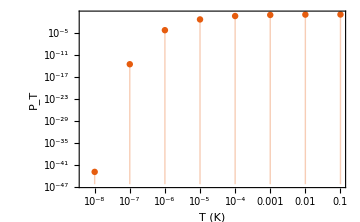

```mathematica
ListLogLogPlot[{{T,Table[Quiet[TransProbC[v]][[Pmaximum]],{v,vs}]}ᵀ}, Filling->Axis, FrameLabel->{"T (K)", "P_T"}]
```

### Zeners' s transition probability (using the diabatic representation)

The probability to cross from one to the other adiabatic potential at an avoided crossing at R_0 is given by
P=exp(-2π (ϵ_12(R_0))^2/(vα(R_0)))  
where v is the atomic velocity given as an external parameter

#### Position of the crossing

```mathematica
CrossingD = Ordering[Abs[dt-df],1][[1]]
```

97

#### α = |H'_11 -H'_22 |

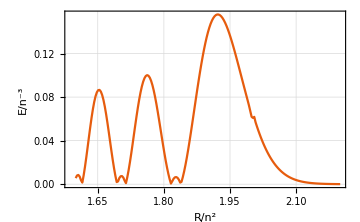

```mathematica
H1 = Interpolation[{R,dt}ᵀ];
H2 = Interpolation[{R,df}ᵀ];
α = Abs[H1'[R]-H2'[R]];
ListLinePlot[{{R,α}ᵀ}]
```

#### off diagonal element ϵ12

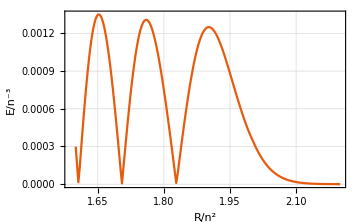

```mathematica
ϵ12 = Abs[do];
ListLinePlot[{{R,ϵ12}ᵀ}]
```

#### Transition Probability

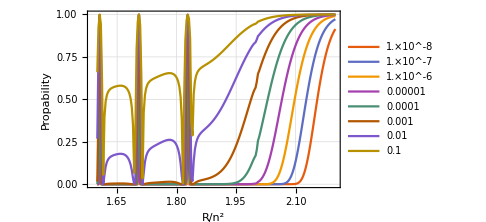

```mathematica
TransProbZ[v_] = Exp[-2π (ϵ12)^2/(v α)/n0];
ListLinePlot[Table[{R,Quiet[TransProbZ[v]]}ᵀ,{v,vs}], PlotLegends->N[T], FrameLabel->{"R/n^2", "Propability"}]
```

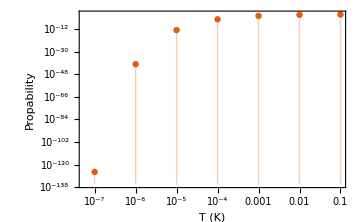

```mathematica
ListLogLogPlot[{{T,Table[Quiet[TransProbZ[v]][[Pmaximum]],{v,vs}]}ᵀ}, Filling->Axis, FrameLabel->{"T (K)", "Propability"}]
```

### Compare Clark and Zener

At the position of the crossing, P_12 and P_LZ should coincide, if the Landau-Zener requirement is met. This is not the case, even far from an exact crossing. It is not clear which requirment is not met. There are three: 
1. R is an external paramter (semi-classical)
2. in the vicinity of the crossing, the diabatic potentials have constant slope
3. in the vicinity of the crossing, the off diagonal element of the diabatic representation is constant

1. should only depend on the temperature
2. and 3. should be valid far from an exact crossing.

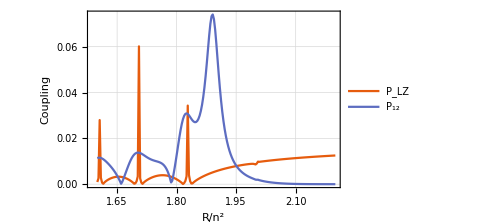

```mathematica
PLZ[t_] = With[{x=α/ϵ12/2/n0^2}, x/(1+x^2 t^2)/2];
ListLinePlot[{{R,PLZ[0]}ᵀ, {R,Abs[P12]}ᵀ}, FrameLabel->{"R/n^2", "Coupling"}, PlotLegends->{"P_LZ","P_12"}]
```

## Numerical calculation of trilobite production rates

### Calculations

#### Grid for n and R

```mathematica
Nvals = Table[i, {i,40,115,1}];
Rvals = Subdivide[16/10, 20/10, 200];
Ivals = Range[Length[Rvals]];
```

#### n dependent diagonalization

```mathematica
H[n_] := Table[Hamiltonian[n, l0, r], {r, Rvals}];
Hamil = ParallelTable[H[n], {n,Nvals}];
Sol = ParallelTable[Eigensystem[Hamil[[i,j]]],{i,Length[Nvals]}, {j,Ivals}];
```

### Results

#### diabatic crossings

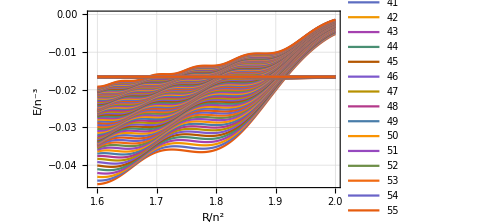

```mathematica
tplot = ListLinePlot[Table[{Rvals,Hamil[[i,All,1,1]]}ᵀ, {i,1,Length[Nvals]}]];
qplot = ListLinePlot[Table[{Rvals,Hamil[[i,All,2,2]]}ᵀ, {i,1,Length[Nvals]}], PlotLegends->Nvals];
Show[tplot,qplot]
```

#### adiabatic potential difference

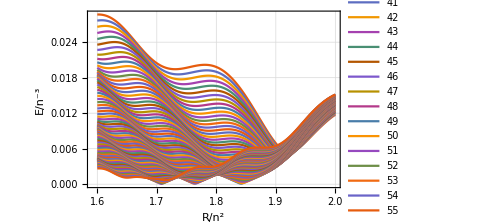

```mathematica
ListLinePlot[Table[{Rvals,Abs[Sol[[i,All,1,1]]-Sol[[i,All,1,2]]]}ᵀ, {i,1,Length[Nvals]}], PlotLegends->Nvals]
```

#### Position of the crossing

```mathematica
CrossingsA = Flatten[Table[Ordering[Abs[Sol[[i,All,1,1]]-Sol[[i,All,1,2]]],1], {i,1,Length[Nvals]}]]
```

{162,161,161,160,160,159,159,158,157,157,156,156,155,155,154,154,153,153,152,152,151,151,150,149,149,148,147,147,146,145,144,143,115,116,117,118,119,120,121,122,123,124,124,125,126,127,128,103,102,101,100,98,77,78,79,80,81,81,82,83,84,85,86,87,88,49,50,51,52,53,54,55,56,57,58,58}

```mathematica
Crossings = Flatten[Table[Ordering[Abs[Hamil[[i,All,1,1]]-Hamil[[i,All,2,2]]],1], {i,1,Length[Nvals]}]]
```

{159,158,158,157,157,157,156,156,155,155,155,154,154,153,153,153,152,152,151,151,151,150,150,149,149,148,148,147,147,146,145,145,144,143,142,141,140,138,136,132,110,107,105,104,103,102,102,101,101,100,99,99,98,98,97,96,95,93,91,74,72,71,70,69,68,68,67,66,66,65,63,60,47,45,44,44}

### Clark

#### d = | ϵ1 - ϵ2 |

```mathematica
dn = Table[Interpolation[Abs[Sol[[i,All,1,1]] - Sol[[i,All,1,2]]]], {i,1,Length[Nvals]}];
```

#### Elements of H

```mathematica
H11n = Table[Interpolation[Hamil[[i,All,1,1]]], {i,1,Length[Nvals]}];
H12n = Table[Interpolation[Hamil[[i,All,1,2]]], {i,1,Length[Nvals]}];
H22n = Table[Interpolation[Hamil[[i,All,2,2]]], {i,1,Length[Nvals]}];
```

#### Derivative H'

```mathematica
DHn[r_] := Table[{{H11n[[i]]'[r],H12n[[i]]'[r]},{H12n[[i]]'[r],H22n[[i]]'[r]}},{i,1,Length[Nvals]}];
```

#### Eigenvectors ϕ

```mathematica
ϕ1n = Table[Interpolation[{Ivals, {Sol[[1,All,2,1,1]], Sol[[1,All,2,1,2]]}ᵀ}ᵀ], {i,1,Length[Nvals]}];
ϕ2n = Table[Interpolation[{Ivals, {Sol[[1,All,2,2,1]], Sol[[1,All,2,2,2]]}ᵀ}ᵀ], {i,1,Length[Nvals]}];
```

#### Off-diagonal element of the P matrix

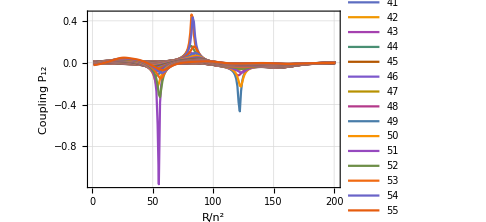

```mathematica
P12n = Table[Interpolation[Table[ϕ1n[[i]][j].DHn[j][[i]].ϕ2n[[i]][j]/dn[[i]][j],{j,1,Length[Ivals]}]],{i,1,Length[Nvals]}];
ListLinePlot[P12n, DataRange->{Rvals[[1]],Rvals[[-1]]}, PlotLegends->Nvals, FrameLabel->{"R/n^2", "Coupling P_12"}]
```

```mathematica
Pmaxima = Flatten[Table[Ordering[Abs[P12n[[i]][Ivals]],-1], {i,1,Length[Nvals]}]]
```

{136,136,137,137,138,138,139,140,140,141,142,143,143,144,144,144,145,144,144,144,144,143,143,142,142,142,142,142,141,141,99,99,99,99,99,99,99,99,98,98,98,98,98,98,97,97,97,96,96,96,95,95,95,53,53,54,55,56,57,57,58,59,60,61,61,62,63,63,64,65,65,66,67,67,68,68,68,69,69,69,69,69,69,69,67,64,1,1,1,1,1,1,1,1,1,1,2,3,3,4,4,5,6,6,7,8,8,9,9,10,11,11,12,13,13,14,14,15,15,17,17}

#### Transition Probability

```mathematica
TP = Table[Quiet[Exp[-2π dn[[i]][Pmaxima[[i]]]/Nvals[[i]]^3/(8*v*Abs[P12n[[i]][Pmaxima[[i]]]])]], {i,1,Length[Nvals]}, {v,vs}];
```

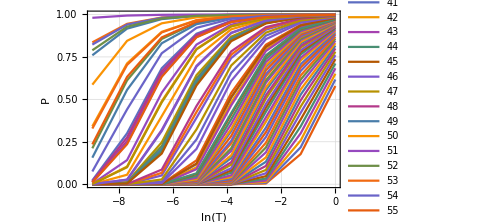

```mathematica
ListLinePlot[TP, FrameLabel->{"ln(T)","P"}, PlotLegends->Nvals, DataRange->{-9,0}]
```

### Zener

#### α = | H'_11 -H'_22 |

```mathematica
H1n = Table[Interpolation[Hamil[[i,All,1,1]]], {i,1,Length[Nvals]}];
H2n = Table[Interpolation[Hamil[[i,All,2,2]]], {i,1,Length[Nvals]}];
αn[r_] = Table[Abs[H1n[[i]]'[r]-H2n[[i]]'[r]], {i,1,Length[Nvals]}];
```

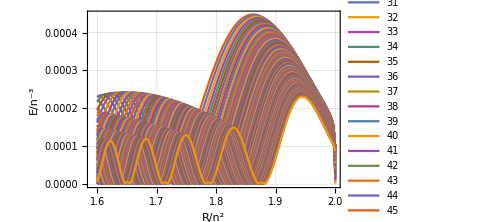

```mathematica
ListLinePlot[αn[Ivals], PlotLegends->Nvals, DataRange->{Rvals[[1]],Rvals[[-1]]}]
```

#### off diagonal element ϵ12

```mathematica
ϵ12n = Table[Interpolation[Abs[Hamil[[i,All,1,2]]]], {i,1,Length[Nvals]}];
```

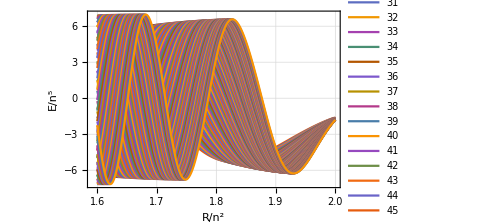

```mathematica
ListLinePlot[Table[Hamil[[i,All,1,2]] Nvals[[i]]^2, {i,1,Length[Nvals]}], FrameLabel-> {"R/n^2","E/n^5"},PlotLegends->Nvals, DataRange->{Rvals[[1]],Rvals[[-1]]}]
```

#### Transition Probability

```mathematica
TPL = Table[Quiet[Exp[-2π ϵ12[[i]][Crossings[[i]]]^2/(v αn[Crossings[[i]]][[i]])/Nvals[[i]]]], {i,1,Length[Nvals]}, {v,vs}];
ListLinePlot[TPL, FrameLabel->{"ln(T)","P"}, PlotLegends->Nvals, DataRange->{-9,0}]
```

-Graphics-

### The coupling at the crossing

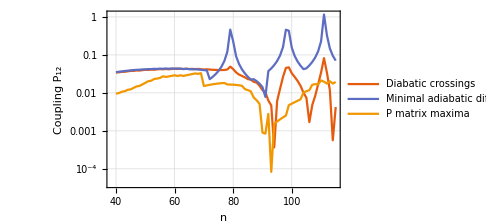

```mathematica
ListLogPlot[{Table[Abs[P12n[[i]][Crossings[[i]]]], {i,1,Length[Nvals]}], Table[Abs[P12n[[i]][CrossingsA[[i]]]], {i,1,Length[Nvals]}], Table[Abs[P12n[[i]][Pmaxima[[i]]]], {i,1,Length[Nvals]}]}, DataRange->{Nvals[[1]],Nvals[[-1]]}, FrameLabel->{"n", "Coupling P_12"}, PlotLegends->{"Diabatic crossings", "Minimal adiabatic difference", "P matrix maxima"}, Joined->True]
```

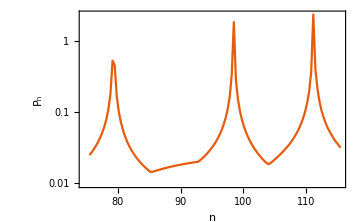

```mathematica
derivplot = ListLogPlot[{Table[Abs[P12n[[i]][Pmaxima[[i]]]], {i,1,Length[Nvals]}]}, DataRange->{Nvals[[1]],Nvals[[-1]]}, FrameLabel->{"n", "P_n"},Joined->True]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/coupling_v2.pdf",derivplot];
```

### Transition Probability using Δ and P_12

#### Trilobite production probability

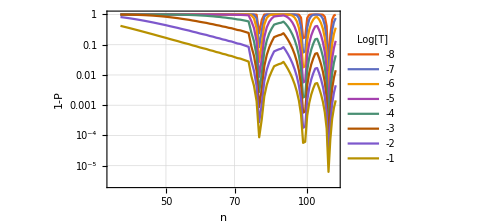

```mathematica
Prob = (1-TP);
ListLogLogPlot[Probᵀ, PlotLegends->LineLegend[Log[10,T], LegendLabel->"Log[T]"], DataRange->{Nvals[[1]], Nvals[[-1]]}, FrameLabel->{"n", "1-P"}, Joined->True]
```

#### Cross section

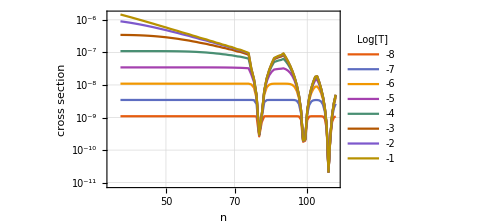

```mathematica
Velocity = vs;
CrossSection = Probᵀ*Velocity;
ListLogLogPlot[CrossSection, PlotLegends->LineLegend[Log[10,T], LegendLabel->"Log[T]"], DataRange->{Nvals[[1]], Nvals[[-1]]}, FrameLabel->{"n", "cross section"}, Joined->True]
```

#### Rate

Here the target area is determined by the position of the crossing

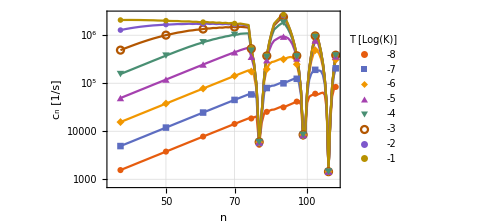

```mathematica
TargetArea = 4π Rvals[[Pmaxima]]^2*Nvals^4;
Density = 1.95*10^12*a0^3*10^6;
Time = ts;
Rate = (Prob*TargetArea)ᵀ*Velocity*Density/Time;
rate = Table[{Nvals[[i]],Rate[[j,i]]},{j,Length[T]},{i,Length[Nvals]}];
rateplot = 
Show[ListLogLogPlot[rate,FrameLabel->{"n", "c_n [1/s]"}, Joined->True ],
ListLogLogPlot[Table[rate[[All,i]],{i,{1,11,21,31,37,40,43,50,56,59,65,72,76}}]ᵀ, PlotMarkers->Automatic,PlotLegends->LineLegend[Log[10,T], LegendLabel->"T [Log(K)]"]]]
```

Here the target area is determined by the semiclassical size of the Rydberg atom 2 n^2

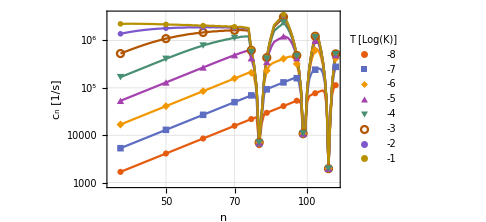

```mathematica
TargetArea = 4π 2^2*Nvals^4;
Rate = (Prob*TargetArea)ᵀ*Velocity*Density/Time;
rate = Table[{Nvals[[i]],Rate[[j,i]]},{j,Length[T]},{i,Length[Nvals]}];
rateplot = 
Show[ListLogLogPlot[rate,FrameLabel->{"n", "c_n [1/s]"}, Joined->True ],
ListLogLogPlot[Table[rate[[All,i]],{i,{1,11,21,31,37,40,43,50,56,59,65,72,76}}]ᵀ, PlotMarkers->Automatic,PlotLegends->LineLegend[Log[10,T], LegendLabel->"T [Log(K)]"]]]
```

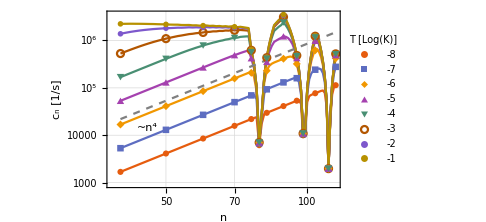

```mathematica
const=Rate[[All,1]]/Nvals[[1]]^4;
Comp = Outer[Times,const,Nvals^4];
comp = Table[{Nvals[[i]],Comp[[j,i]]},{j,Length[T]},{i,Length[Nvals]}];
rateplot = 
Show[ListLogLogPlot[rate, FrameLabel->{"n", "c_n [1/s]"},Joined->True ],
ListLogLogPlot[{comp[[3,All,1]],1.3comp[[3,All,2]]}ᵀ, Joined->True, PlotStyle->{Gray,Dashed},PlotLabels->Placed["~n^4",Below]],
ListLogLogPlot[Table[rate[[All,i]],{i,{1,11,21,31,37,40,43,50,56,59,65,72,76}}]ᵀ, PlotMarkers->Automatic,PlotLegends->LineLegend[Log[10,T], LegendLabel->"T [Log(K)]"]]]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/rateRb_v9.pdf",rateplot];
```

The position of the crossing is however not a unique quantity. Shown here are the position of the diabatic crossing and the position where the derivative coupling element has a local maximum.

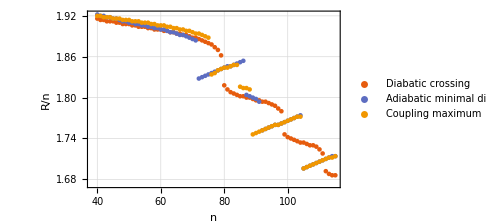

```mathematica
ListPlot[{{Nvals,Rvals[[Crossings]]}ᵀ,{Nvals,Rvals[[CrossingsA]]}ᵀ,{Nvals,Rvals[[Pmaxima]]}ᵀ }, FrameLabel->{"n","R/n"}, PlotLegends->{"Diabatic crossing", "Adiabatic minimal difference", "Coupling maximum"}]
```

## Conical Intersection

### 2 D Plots

#### Calculations

```mathematica
Nvals = Table[i, {i,40,70,10}];
Rvals = Subdivide[16/10, 22/10, 100];
Ivals = Range[Length[Rvals]];
```

```mathematica
H[n_] := Table[Hamiltonian[n, l0, r], {r, Rvals}];
Hamil = ParallelTable[H[n], {n,Nvals}];
Sol = ParallelTable[Eigensystem[Hamil[[i,j]]],{i,Length[Nvals]}, {j,Ivals}];
```

```mathematica
PES = ParallelTable[With[{H=Hamil[[i,j]], n=Nvals[[i]],δ=Δ[Nvals[[i]]]},{H[[1,1]],n^3 δ+n^2/1000H[[1,2]],H[[2,2]]}],{i,Length[Nvals]}, {j,Ivals}];
```

#### Plots

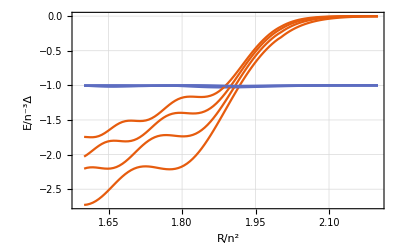

```mathematica
diaplot = Show[Table[ListLinePlot[PES[[i,All,1;;-1;;2]]ᵀ/δ[l0-1],DataRange->{1.6,2.2}, FrameLabel -> {"R/n^2", "E/n^-3Δ"}],{i,Length[Nvals]}], ImageSize->400]
```

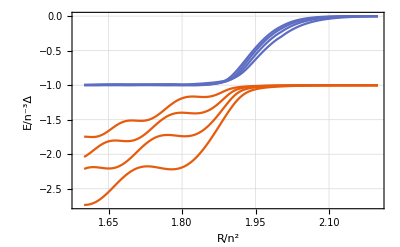

```mathematica
adiplot = Show[Table[ListLinePlot[Sol[[i,All,1,All]]ᵀ/δ[l0-1],DataRange->{1.6,2.2}, FrameLabel -> {"R/n^2", "E/n^-3Δ"}],{i,Length[Nvals]}],ImageSize->400]
```

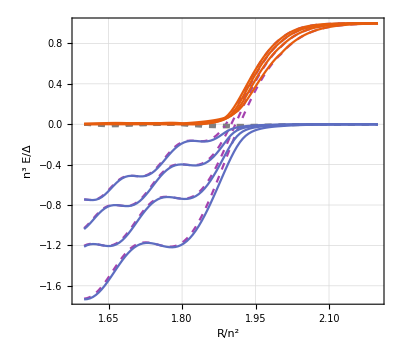

```mathematica
bothplot = Show[Table[ListLinePlot[PES[[i,All,1;;-1;;2]]ᵀ/δ[l0-1]+1,DataRange->{1.6,2.2}, FrameLabel -> {"R/n^2", "n^3 E/Δ"},PlotStyle->{Directive[ColorData[108, "ColorList"][[4]],Dashed],Directive[Gray,Dashed]}],{i,Length[Nvals]}],Table[ListLinePlot[Sol[[i,All,1,All]]ᵀ/δ[l0-1]+1,DataRange->{1.6,2.2}, FrameLabel -> {"R/n^2", "E/n^-3Δ"},PlotStyle->{Directive[ColorData[108, "ColorList"][[2]]],Directive[ColorData[108, "ColorList"][[1]]]}],{i,Length[Nvals]}], ImageSize->400, AspectRatio->0.9]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/diabatic_v2.pdf",diaplot];
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/adiabatic_v2.pdf",adiplot];
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/bothabatic_v8.pdf",bothplot];
```

#### Other regime

```mathematica
Nvals = Table[i, {i,97.01,99.01,1}];
Rvals = Table[i,{i,17/10,185/100,1/1000}];
Ivals = Range[Length[Rvals]];
```

```mathematica
H[n_] := Table[Hamiltonian[n,r], {r, Rvals}];
Hamil = ParallelTable[H[n], {n,Nvals}];
Sol = ParallelTable[Eigensystem[Hamil[[i,j]]],{i,Length[Nvals]}, {j,Ivals}];
```

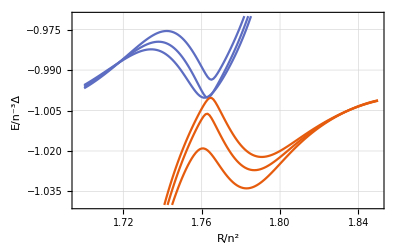

```mathematica
NcutPlot = Show[Table[ListLinePlot[Evaluate@Table[Sol[[i,All,1,j]],{j,2}]/δ[l0-1],DataRange->{1.7,1.85},PlotRange->{-1.04,-0.97},FrameLabel -> {"R/n^2", "E/n^-3Δ"}], {i,Length[Nvals]}], ImageSize->400]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/ncut.pdf", NcutPlot];
```

### 3D Plots

#### Calculations

```mathematica
Nvals = Table[i, {i,75.5,115.5,1/3}];
Rvals = Table[i,{i,17/10,19/10,1/1000}];
Ivals = Range[Length[Rvals]];
```

```mathematica
Hamiltonian[n_,  r_] := With[{a=2π A[kin[r n^2,n]], t=Trilobite[n,r n^2], f=q[n,l0,r n^2], e=Δ[n]}, n^3 a {{t^2, t f}, {t f, e/a+f^2}}]
H[n_] := Table[Hamiltonian[n, r], {r, Rvals}];
Hamil = ParallelTable[H[n], {n,Nvals}];
Sol = ParallelTable[Eigensystem[Hamil[[i,j]]],{i,Length[Nvals]}, {j,Ivals}];
```

#### Plots

```mathematica
R1=20;
R2=110;
N1=50;
N2=90;
a = 1.6;
θ = -2.38;
ticks = Join[Table[{1.72+i,1.72+i,{0.02,0}},{i,0,0.08,0.04}],Table[{1.74+i,,{0.02,0}},{i,0,0.06,0.04}], Table[{1.73+i,,{0.01,0}},{i,0,0.07,0.02}], Table[{1.725+i,,{0.01,0}},{i,0,0.075,0.02}],Table[{1.735+i,,{0.01,0}},{i,0,0.065,0.02}]];
InsetPlot = ListPlot3D[Evaluate@Table[Sol[[N1;;N2,R1;;R2,1,i]], {i,2}]/δ[l0-1]+1, PlotRange->{-0.05,0.05},DataRange->{{Rvals[[R1]],Rvals[[R2]]},{Nvals[[N1]],Nvals[[N2]]}},AxesLabel-> None, Ticks->{ticks,Automatic,Automatic}, AxesEdge->{{0,1},{0,1},{1,0}}, Mesh->{0,15},ViewPoint->{a Cos[θ],a Sin[θ],-0.05}, AspectRatio->1,PlotStyle->106,ImageSize->300]
```

-Graphics3D-

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/3D_small_v4.pdf", InsetPlot];
```

```mathematica
a = 1.6;
θ = -2.38;
SurfPlot = ListPlot3D[Evaluate@Table[Sol[[All,All,1,i]], {i,2}]/δ[l0-1]+1, PlotRange->{-0.15,0.2},DataRange->{{Rvals[[1]],Rvals[[-1]]},{Nvals[[1]],Nvals[[-1]]}},AxesLabel-> None,  AxesEdge->{{0,0},{0,0},{0,1}}, Mesh->{0,40},ViewPoint->{a Cos[θ],a Sin[θ],-0.05}, AspectRatio->1,PlotStyle->106,ImageSize->500]
```

-Graphics3D-

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/3D_large_v2.pdf", SurfPlot];
```

```mathematica
ListPlot3D[{Hamil[[All,All,1,1]],Hamil[[All,All,2,2]],Hamil[[All,All,1,2]]+Hamil[[All,-1,2,2]]}, DataRange->{{Rvals[[1]],Rvals[[-1]]},{Nvals[[1]],Nvals[[-1]]}}, PlotRange->{-0.019,-0.0135}, Mesh->{0,40}, ViewPoint->{a Cos[θ],a Sin[θ],0.1}, AspectRatio->1]
```

-Graphics3D-

#### 2 D cuts at R_0

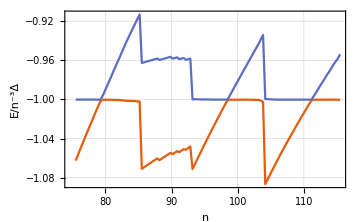

```mathematica
RcutPlot = ListLinePlot[Evaluate@Table[Table[Sol[[i,Pmaxima[[i]],1,j]],{i,Length[Nvals]}],{j,2}]/δ[l0-1],DataRange->{Nvals[[1]],Nvals[[-1]]}, FrameLabel -> {"n", "E/n^-3Δ"}]
```

```mathematica
Export["/home/frederic/Documents/paper/fstates/plots/rcut.pdf", RcutPlot];
```

### Prediction of resonances

#### Conditions for exact crossing

1) f wave function has a root
2) trilobite potential energy equals quantum defect energy

```mathematica
He={{t^2,t f}, {t f,f^2-Q}};
Eigenvalues[He]
Eigenvalues[He]/.{f->0}//FullSimplify
Eigenvalues[He]/.{f->0,t^2->Q}//FullSimplify
```

{1/2 (f^2-Q+t^2-√(4 Q t^2+(-f^2+Q-t^2)^2)),1/2 (f^2-Q+t^2+√(4 Q t^2+(-f^2+Q-t^2)^2))}

{1/2 (-Q+t^2-√((Q+t^2)^2)),1/2 (-Q+t^2+√((Q+t^2)^2))}

{-√(Q^2),√(Q^2)}

#### Roots of the f wave function

```mathematica
N0 = Table[n,{n,60,120}];
```

```mathematica
Sol[n_] := Solve[U[n,l0-1,r n^2]==0 && 1.0<r<2.0, r]
R1 = Table[{n,r/.Quiet[Sol[n][[-1]]]}, {n,N0}];
R2 = Table[{n,r/.Quiet[Sol[n][[-2]]]}, {n,N0}];
R3 = Table[{n,r/.Quiet[Sol[n][[-3]]]}, {n,N0}];
```

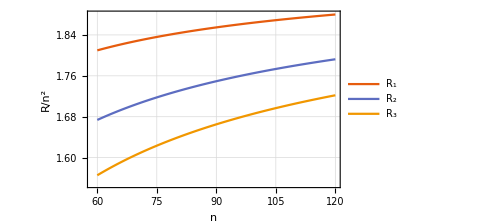

```mathematica
ListLinePlot[{R1,R2,R3}, FrameLabel->{"n","R/n^2"}, PlotLegends->{"R_1","R_2","R_3"}]
```

#### Trilobite wave function and quantum defect

```mathematica
Res[pos_] := Table[With[{n=pos[[i,1]],r=pos[[i,2]]},{n,2π A[kin[r n^2,n]]Trilobite[n,l0,r n^2]^2 n^3}],{i,Length[pos]}]
```

```mathematica
ΔPos = Table[{n,Δ[n] n^3}, {n,N0}];
```

```mathematica
ResPos = Table[Res[i],{i,{R1,R2,R3}}];
```

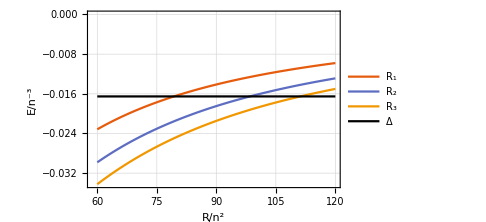

```mathematica
Show[
ListLinePlot[ResPos,PlotLegends->{"R_1","R_2","R_3"}],
ListLinePlot[ΔPos, PlotLegends->{"Δ"}, PlotStyle->Black]]
```

### Resonance positions depending on species

#### lithium

none for the p state

for the d state around 200

#### sodium

d state

```mathematica
Flatten[Table[N0[[Ordering[Abs[ResPos[[i,All,2]]-ΔPos[[All,2]]],1]]], {i,3}]]
```

{31,38,44}

#### potassium

f state

```mathematica
Flatten[Table[N0[[Ordering[Abs[ResPos[[i,All,2]]-ΔPos[[All,2]]],1]]], {i,2}]]
```

{116,144}

#### rubidium

f state

```mathematica
Flatten[Table[N0[[Ordering[Abs[ResPos[[i,All,2]]-ΔPos[[All,2]]],1]]], {i,3}]]
```

{79,98,111}

#### cesium

s state

```mathematica
Flatten[Table[N0[[Ordering[Abs[ResPos[[i,All,2]]-ΔPos[[All,2]]],1]]], {i,3}]]
```

{43,54,61}

f state

```mathematica
Flatten[Table[N0[[Ordering[Abs[ResPos[[i,All,2]]-ΔPos[[All,2]]],1]]], {i,3}]]
```

{61,75,85}

#### strontium

none, the quantum defects are inadequate

## Compare potentials to full-spin diagonalization

### Import data

```mathematica
grid = Flatten[Import["/home/frederic/Documents/Wolfram Mathematica/data/79f_grid.csv","Data"],1]/n0^2;
```

```mathematica
curves = Import["/home/frederic/Documents/Wolfram Mathematica/data/79f_Ω=2.5.csv","Data"][[All,164;;168]];
```

### Plot

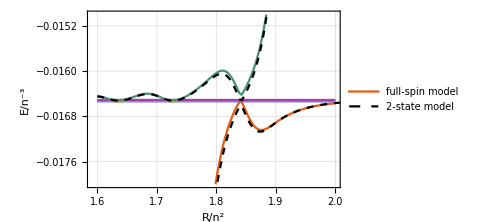

```mathematica
compare = Show[ListLinePlot[Evaluate@Table[{grid,curves[[All,i]]}ᵀ,{i,5}], PlotRange->{-0.018,-0.015}, PlotLegends->{"full-spin model"}],
ListLinePlot[{{R, at}ᵀ, {R, af}ᵀ}, PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotLegends->{"2-state model"}]]
```

```mathematica
Export["/home/frederic/Documents/Wolfram Mathematica/data/compare.pdf", compare];
```